# AlternatingTreeGraph

Construct an alternating tree graph

## Definition

```mathematica
AlternatingTreeGraph[n_,options:OptionsPattern[Graph]]:=Block[{pathgraph,top,bottom},pathgraph=PathGraph[Range[n]];top=UndirectedEdge@@@Transpose[{Range[2,n-1],Range[1+n,2(-1+n)]}];bottom=UndirectedEdge@@@Transpose[{Range[2,n-1],Range[5+2(-3+n),5+3 (-3+n)]}];EdgeAdd[pathgraph,Join[top,bottom],options,GraphLayout->"SpringElectricalEmbedding"]]
```

## Documentation

### Usage

AlternatingTreeGraph[n]

generates an alternating tree graph from a path graph with n nodes.

### Details & Options

According to the paper Paths, Trees, and Flowers by Edmonds, "An alternating tree J is a tree each of whose edges joins an inner vertex to an outer vertex so that each inner vertex of J meets exactly two edges of /.
An alternating tree contains one more outer vertex than inner vertices. This follows
from the third definition of tree by regarding each inner vertex with its two
edges as a single edge joining two outer vertices."

The graph layout is SpringElectricalEmbedding by default.

The function has the same options as Graph.

## Examples

### Basic Examples

Make an alternating tree graph with 10 nodes:

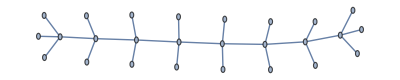

```mathematica
AlternatingTreeGraph[10]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

#### GraphLayout

All graph layouts can be selected:

```mathematica
Table[Labeled[AlternatingTreeGraph[10,GraphLayout->embedding],embedding],{embedding,{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","StarEmbedding","BallonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}}]
```

-Graphics-

Try SpringEmbedding if SpringElectricalEmbedding does not work well:

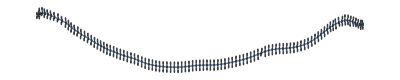

```mathematica
AlternatingTreeGraph[100]
```

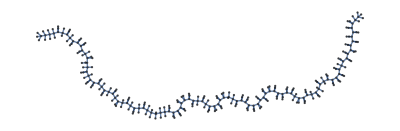

```mathematica
AlternatingTreeGraph[100,GraphLayout->"SpringEmbedding"]
```

Compare and contrast graph layouts for a large alternating tree:

```mathematica
Table[Labeled[AlternatingTreeGraph[200,GraphLayout->embedding],embedding],{embedding,{"BipartiteEmbedding","CircularEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","StarEmbedding","BallonEmbedding","RadialEmbedding","LayeredEmbedding","GravityEmbedding","HighDimensionalEmbedding","SpectralEmbedding","SphericalEmbedding","SpringElectricalEmbedding","SpringEmbedding","TutteEmbedding"}}]
```

-Graphics-

### Applications

Find the graph center and graph periphery:

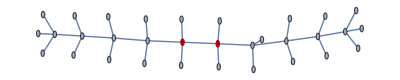

```mathematica
HighlightGraph[AlternatingTreeGraph[12],GraphCenter[AlternatingTreeGraph[12]]]
```

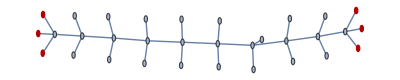

```mathematica
HighlightGraph[AlternatingTreeGraph[12],GraphPeriphery[AlternatingTreeGraph[12]]]
```

### Properties and Relations

Use FindSequenceFunction to find a pattern in the order and size of the graph:

```mathematica
VertexCount/@AlternatingTreeGraph/@Range[4,20]
```

{8,11,14,17,20,23,26,29,32,35,38,41,44,47,50,53,56}

```mathematica
FindSequenceFunction[VertexCount/@AlternatingTreeGraph/@Range[4,20]]
```

5+3 #1&

```mathematica
FindSequenceFunction[EdgeCount/@AlternatingTreeGraph/@Range[4,20]]
```

4+3 #1&

Predict the size of a 2980 length alternating tree:

```mathematica
FindSequenceFunction[VertexCount/@AlternatingTreeGraph/@Range[4,20]][2980]
```

8945

```mathematica
FindSequenceFunction[EdgeCount/@AlternatingTreeGraph/@Range[4,20]][2980]
```

8944

We can see the number of edges is always 1 less than the number of nodes.

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Burbery

### Keywords

trees

graphs

blossom inequalities

arc routing

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

PathGraph

KaryTree

CompleteKaryTree

TreeGraph

StarGraph

Tree

### Related Resource Objects

UndirectedGraphToMixedGraph

SynonymGraph

WordGraph

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.1+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.